#### Kirill Zakharov Pade Approximation

```mathematica
Clear[padeApprox]
```

```mathematica
funD[fun_,y_,k_,h_]:=D[fun[y],{y,k}]/.y-> h
```

fun - функция
x0 - начальное приближение
m - число итераций
ξ - точность решения

```mathematica
padeApprox[fun_,x0_,m_,ξ_]:=Module[{t,x=x0,array={},iter},Do[If[fun[x]<ξ,Break[],
t=(-fun[x])/funD[fun,k,i,x];x=x^2/(x-t);AppendTo[array,x]],
{i,1,m}];N/@array]
```

#### Пример 1

```mathematica
fun1[y_]:=ⅇ^y-2
```

```mathematica
test1=padeApprox[fun1,1,20,0.001]
```

{0.790988,0.707607,0.693537}

```mathematica
test2=padeApprox[fun1,1,20,0.0001]
```

{0.790988,0.707607,0.693537,0.693147}

Итерация, при которой достигли заданной точности

```mathematica
test2//Length
```

4

#### Проверка

```mathematica
Log[2]//N
```

0.693147

Невязка

```mathematica
fun1[test2//Last]
```

5.88707×10^-7

#### Пример 2

```mathematica
fun[y_]:=y^3+6 y^2+9y-4
```

```mathematica
lst=padeApprox[fun,3.6,3,0.01]
```

{2.45556,1.19643,0.354205}

#### Ответ

```mathematica
lst⟦3⟧
```

0.354205

Итерация, при которой достигли заданной точности

```mathematica
lst//Length
```

3

Невязка

```mathematica
fun[lst⟦3⟧]
```

-0.0149463

#### Визуальное представление

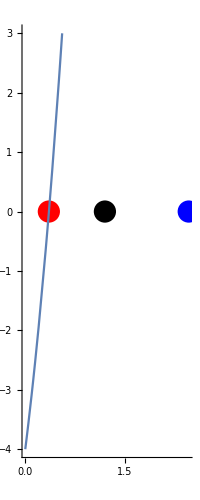

```mathematica
Show[Graphics[{PointSize[0.04],Blue,Point[{lst⟦1⟧,0}],Black,Point[{lst⟦2⟧,0}],Red,Point[{lst⟦3⟧,0}]},Axes->True],Plot[x^3+6 x^2+9x-4,{x,-5,5},PlotRange->{Automatic,{-4,3}}]]
```

#### Проверка

```mathematica
Solve[x^3+6 x^2+9x-4==0,x]
```

{{x→Root0.355Root[-4+9 #1+6 #1^2+#1^3&,1]0.3553013976081199},{x→Root-3.18-1.08 ⅈRoot[-4+9 #1+6 #1^2+#1^3&,2]-3.1776506988040603},{x→Root-3.18+1.08 ⅈRoot[-4+9 #1+6 #1^2+#1^3&,3]-3.1776506988040603}}